## setup

### overhead

```mathematica
(* clear all variable names and assignments *)
Clear["Global`*"];ClearAll["Global`*"];Remove["Global`*"];ClearSystemCache[];
```

```mathematica
(* directory of Mathematica files *)
dirMathematica=Environment["HOME"]<>"/Mathematica_files/";

(* ln-fhs "/Users/dantopa/Dropbox/_mm" "/Users/dantopa/Mathematica_files" *)
(* packages shared by all notebooks *)
dirnb=dirMathematica<>"nb/";
dirPack=dirnb<>"packages/";

(* seed file *)
nbSeed="seed 19_12.nb";
```

### tag

```mathematica
home="ert/rcs/sphere/";  
Get["utility modules.m",Path->dirPack];
stamp1;
```

CreateDirectory::filex: /Users/dantopa/Mathematica_files/io/ already exists.

CreateDirectory::filex: /Users/dantopa/Dropbox/_mm/io/ert/ already exists.

CreateDirectory::filex: /Users/dantopa/Dropbox/_mm/io/ert/rcs/ already exists.

General::stop: Further output of CreateDirectory::filex will be suppressed during this calculation.

maximum memory: 0.184529 GB

seed file: /Users/dantopa/Mathematica_files/nb/seed 19_12.nb

user: dantopa, CPU: Xiuhcoatl,  MM v. 12.1.0 for Mac OS X x86

date: Jul 7, 2020, time: 17:50:56

nb: /Users/dantopa/Mathematica_files/nb/ert/rcs/sphere/sphere-01.nb

### modules, functions, settings, ...

#### admin

```mathematica
printmem
```

maximum memory: 0.184529 GB

```mathematica
(* save notebook *)
NotebookSave[EvaluationNotebook[]];
```

#### settings

```mathematica
exportFlag=True;
```

```mathematica
o={0,0};
```

```mathematica
guc=Circle[o,1];
```

```mathematica
ipad=ImagePadding->{{Automatic,3},{Automatic,Automatic}};
```

```mathematica
isize=ImageSize->5 72;
```

#### functions

#### substitutions

#### modules

## 1

https : // mathematica.stackexchange.com/questions/73354/triangular - mesh - of - random - points - on - a - sphere

```mathematica
reg=DiscretizeGraphics[Sphere[],MaxCellMeasure->{"Length"->√(8/3)}]
MeshCellCount[reg]
```

{12,30,20}

```mathematica
reg=DiscretizeGraphics[Sphere[{0,0,0},50],MaxCellMeasure->{"Length"->0.25}]
MeshCellCount[reg]
```

{163842,491520,327680}

```mathematica
MeshCellCount[reg]
```

{10242,30720,20480}

## 2

```mathematica
msh={0,0,0};
mshContainer={};
area={};
steps={};
index=0;
ρ=10/2;
Do[
(* generate discretization *)
reg=DiscretizeGraphics[Sphere[{0,0,0},ρ],MaxCellMeasure->{"Length"->k}];
(* vertex, edge, face *)
mshcnt=MeshCellCount[reg];
(* new entry? *)
If[mshcnt==msh,Continue[]];
Print["new mesh at edge length ",k];
index++;
msh=mshcnt;mshContainer=AppendTo[mshContainer,mshcnt];
area=AppendTo[area,Area[reg]/(4π)];
steps=AppendTo[steps,k];
filename=dirData<>"sphere-d"<>pad[ρ,3]<>"-"<>pad[index]<>".obj";
Export[filename,reg];
multiExport["sphere-"<>pad[ρ,3]<>"-"<>pad[index],reg];
,{k,75,0.05,-0.05}];
mshContainer
area
steps
```

new mesh at edge length 75.

new mesh at edge length 5.25

new mesh at edge length 2.7

new mesh at edge length 1.25

new mesh at edge length 0.55

new mesh at edge length 0.25

new mesh at edge length 0.1

new mesh at edge length 0.05

{{12,30,20},{42,120,80},{162,480,320},{642,1920,1280},{2562,7680,5120},{10242,30720,20480},{40962,122880,81920},{163842,491520,327680}}

{19.0479,23.2086,24.5302,24.8811,24.9702,24.9925,24.9981,24.9995}

{75.,5.25,2.7,1.25,0.55,0.25,0.1,0.05}

```mathematica
dirData
```

/Users/dantopa/Mathematica_files/io/ert/rcs/sphere/data/

## resolutions

### 5 m

{{12,30,20},{42,120,80},{162,480,320},{642,1920,1280},{2562,7680,5120},{10242,30720,20480},{40962,122880,81920},{163842,491520,327680}}

{19.0479,23.2086,24.5302,24.8811,24.9702,24.9925,24.9981,24.9995}

{15.,5.25,2.7,1.25,0.55,0.25,0.1,0.05}

### 50 m

{{12,30,20},{42,120,80},{162,480,320},{642,1920,1280},{2562,7680,5120},{10242,30720,20480},{40962,122880,81920},{163842,491520,327680},{655362,1966080,1310720},{2621442,7864320,5242880}}

{1904.79,2320.86,2453.02,2488.11,2497.02,2499.25,2499.81,2499.95,2499.99,2500.}

{75.,52.55,27.3,12.8,5.8,2.6,1.15,0.5,0.2,0.1}

## list

### list

```mathematica
ρ=100;
hdr="./facimusFacet ../obj/";
Do[
str=hdr<>"sphere-"<>pad[ρ,3]<>"-"<>pad[k]<>".obj";
Print["new_step '",str,"'"];
Print["          ",str];
,{k,7}]
```

new_step './facimusFacet ../obj/sphere-100-01.obj'

./facimusFacet ../obj/sphere-100-01.obj

new_step './facimusFacet ../obj/sphere-100-02.obj'

./facimusFacet ../obj/sphere-100-02.obj

new_step './facimusFacet ../obj/sphere-100-03.obj'

./facimusFacet ../obj/sphere-100-03.obj

new_step './facimusFacet ../obj/sphere-100-04.obj'

./facimusFacet ../obj/sphere-100-04.obj

new_step './facimusFacet ../obj/sphere-100-05.obj'

./facimusFacet ../obj/sphere-100-05.obj

new_step './facimusFacet ../obj/sphere-100-06.obj'

./facimusFacet ../obj/sphere-100-06.obj

new_step './facimusFacet ../obj/sphere-100-07.obj'

./facimusFacet ../obj/sphere-100-07.obj

## manipulate data

```mathematica
mshContainer={{12,30,20},{42,120,80},{162,480,320},{642,1920,1280},{2562,7680,5120},{10242,30720,20480},{40962,122880,81920},{163842,491520,327680}};
area={19.047944862324506,23.208633084536068,24.53016946510168,24.88111397981108,24.97018998884801,24.992542060757653,24.99813518038361,24.999533774396134}/25;
```

```mathematica
faces=mshContainer[[All,3]];
z={faces,area}ᵀ
```

{{20,0.761918},{80,0.928345},{320,0.981207},{1280,0.995245},{5120,0.998808},{20480,0.999702},{81920,0.999925},{327680,0.999981}}

```mathematica
g001=Graphics[{Blue,Line[{{Log[10],Log[1]},{Log[2000000],Log[1]}}]}];
```

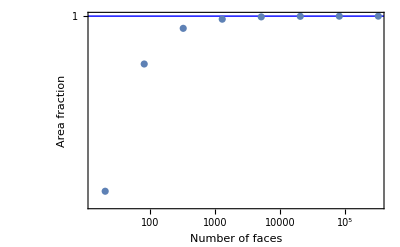

```mathematica
g000=ListLogLogPlot[z,
FrameLabel->{"Number of faces","Area fraction"},
Frame->True];
gsphere=Show[{g000,g001}]
```

## end

```mathematica
(* save notebook *)
NotebookSave[EvaluationNotebook[]];
```